Get the photon flux of generic spectrum. PPPC uses GeV. Output should be MeV to match the Fermi analysis.

```mathematica
Get["/Users/austingottfredson/Indirect-Dark-Matter-Detection/dlNdlxEW.m"];
```

```mathematica
mdm=1000;             (* GeV *)
primary="b";
j0=10^18;           (* GeV^2/cm^5. Update this to be the actual J-factor and change main.py accordingly. *)
sigmav0=10^-25 (* cm^3/s *)
```

```mathematica
dndlx[mdm_,primary_]:=With[{i:=10^xp},Table[{i mdm*1000,10^(dlNdlxIEW[primary->"γ"][mdm,Log[10,i]])},{xp,-7,0,.1}]];
```

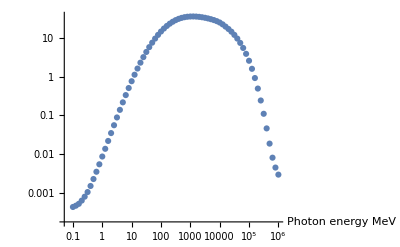

```mathematica
ListLogLogPlot[dndlx[mdm,primary],AxesLabel->{"Photon energy MeV"}]
```

photonflux will give the specfile needed to upload to the python file

```mathematica
photonflux[mdm_,primary_]:=Table[{dndlx[mdm,primary][[n,1]],1/(4 Pi)sigmav0/(2 mdm^2) dndlx[mdm,primary][[n,2]] j0},{n,1,Length[dndlx[mdm,primary]]}]
```

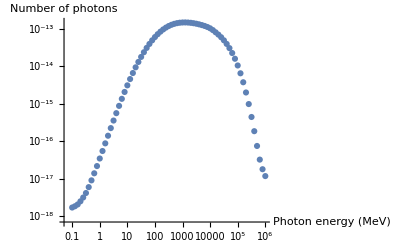

```mathematica
ListLogLogPlot[photonflux[mdm,primary],AxesLabel->{"Photon energy (MeV)","Number of photons"}]
```

eflux multiplies the spectrum by k (kinetic energy of photon) to get energy flux

```mathematica
eflux[mdm_,primary_]:=Table[{dndlx[mdm,primary][[n,1]],1/(4 Pi)sigmav0/(2 mdm^2) dndlx[mdm,primary][[n,2]]*dndlx[mdm,primary][[n,1]] j0},{n,1,Length[dndlx[mdm,primary]]}]
```

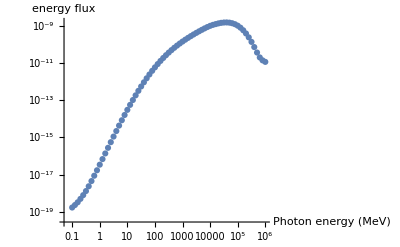

```mathematica
ListLogLogPlot[eflux[mdm,primary],AxesLabel->{"Photon energy (MeV)","energy flux"}]
```

```mathematica
Export[NotebookDirectory[] <> "specfile.txt", photonflux[mdm,primary], "Table"]
```

/Users/austingottfredson/Indirect-Dark-Matter-Detection/specfile.txt